# Graphs of countries

Author Name

Abstract

## Eurasia

XXXX:

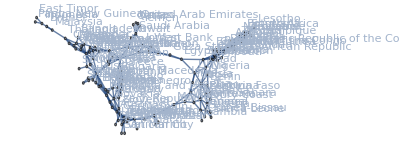

```mathematica
Eurasia=SimpleGraph@NestGraph[#["BorderingCountries"]&,Entity["Country","Switzerland"],13,VertexLabels->Automatic,ImageSize->Full,DirectedEdges->False]
```

Find the greatest distance a country is from another country

```mathematica
GraphDiameter[Eurasia]
```

18

One country is at most 18 country borders and crossings away from another country.

Which countries are the farthest away? We can use GraphPeriphery?

```mathematica
GraphPeriphery[Eurasia]
```

{East Timor,Papua New Guinea,Lesotho}

```mathematica
EccentricityPlot[g_?GraphQ]:=
Module[{ve=Table[VertexEccentricity[g,v],{v,VertexList[g]}]},
HighlightGraph[g,Table[Style[v,ColorData["TemperatureMap",ve⟦VertexIndex[g,v]⟧/Max[ve]]],{v,VertexList[g]}]]
];
```

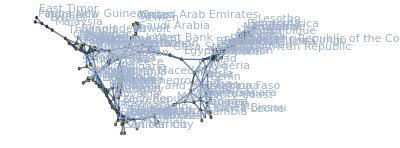

```mathematica
EccentricityPlot[Eurasia]
```

```mathematica
GraphRadius[Eurasia]
```

9

```mathematica
GraphCenter[Eurasia]
```

{Syria,Jordan}

The countries with the most central location are Syria and Jordan.

Cross every country border once

```mathematica
First@FindPostmanTour[Eurasia]
```

{Switzerland<->Liechtenstein,Liechtenstein<->Austria,Austria<->Slovenia,Slovenia<->Croatia,Croatia<->Montenegro,Montenegro<->Albania,Albania<->Greece,Greece<->Turkey,Turkey<->Syria,Syria<->Lebanon,Lebanon<->Israel,Israel<->West Bank,West Bank<->Jordan,Jordan<->Saudi Arabia,Saudi Arabia<->Yemen,Yemen<->Oman,Oman<->United Arab Emirates,United Arab Emirates<->Saudi Arabia,Saudi Arabia<->Qatar,Qatar<->Saudi Arabia,Saudi Arabia<->Oman,Oman<->Saudi Arabia,Saudi Arabia<->Kuwait,Kuwait<->Iraq,Iraq<->Saudi Arabia,Saudi Arabia<->Jordan,Jordan<->Israel,Israel<->Gaza Strip,Gaza Strip<->Egypt,Egypt<->Sudan,Sudan<->South Sudan,South Sudan<->Uganda,Uganda<->Tanzania,Tanzania<->Mozambique,Mozambique<->Eswatini,Eswatini<->South Africa,South Africa<->Lesotho,Lesotho<->South Africa,South Africa<->Zimbabwe,Zimbabwe<->Botswana,Botswana<->South Africa,South Africa<->Mozambique,Mozambique<->South Africa,South Africa<->Namibia,Namibia<->Botswana,Botswana<->Zambia,Zambia<->Zimbabwe,Zimbabwe<->Mozambique,Mozambique<->Malawi,Malawi<->Mozambique,Mozambique<->Zambia,Zambia<->Malawi,Malawi<->Tanzania,Tanzania<->Rwanda,Rwanda<->Burundi,Burundi<->Tanzania,Tanzania<->Zambia,Zambia<->Namibia,Namibia<->Angola,Angola<->Zambia,Zambia<->Democratic Republic of the Congo,Democratic Republic of the Congo<->Tanzania,Tanzania<->Kenya,Kenya<->Uganda,Uganda<->Rwanda,Rwanda<->Democratic Republic of the Congo,Democratic Republic of the Congo<->Burundi,Burundi<->Democratic Republic of the Congo,Democratic Republic of the Congo<->Angola,Angola<->Republic of the Congo,Republic of the Congo<->Gabon,Gabon<->Republic of the Congo,Republic of the Congo<->Democratic Republic of the Congo,Democratic Republic of the Congo<->Uganda,Uganda<->Kenya,Kenya<->Somalia,Somalia<->Djibouti,Djibouti<->Somalia,Somalia<->Ethiopia,Ethiopia<->Kenya,Kenya<->South Sudan,South Sudan<->Democratic Republic of the Congo,Democratic Republic of the Congo<->Central African Republic,Central African Republic<->Republic of the Congo,Republic of the Congo<->Cameroon,Cameroon<->Gabon,Gabon<->Equatorial Guinea,Equatorial Guinea<->Cameroon,Cameroon<->Central African Republic,Central African Republic<->South Sudan,South Sudan<->Ethiopia,Ethiopia<->Djibouti,Djibouti<->Eritrea,Eritrea<->Ethiopia,Ethiopia<->Sudan,Sudan<->Eritrea,Eritrea<->Sudan,Sudan<->Central African Republic,Central African Republic<->Chad,Chad<->Cameroon,Cameroon<->Nigeria,Nigeria<->Benin,Benin<->Togo,Togo<->Ghana,Ghana<->Togo,Togo<->Burkina Faso,Burkina Faso<->Ghana,Ghana<->Ivory Coast,Ivory Coast<->Liberia,Liberia<->Sierra Leone,Sierra Leone<->Guinea,Guinea<->Guinea-Bissau,Guinea-Bissau<->Senegal,Senegal<->Gambia,Gambia<->Senegal,Senegal<->Guinea,Guinea<->Liberia,Liberia<->Ivory Coast,Ivory Coast<->Guinea,Guinea<->Mali,Mali<->Ivory Coast,Ivory Coast<->Burkina Faso,Burkina Faso<->Benin,Benin<->Niger,Niger<->Nigeria,Nigeria<->Chad,Chad<->Sudan,Sudan<->Libya,Libya<->Chad,Chad<->Niger,Niger<->Burkina Faso,Burkina Faso<->Mali,Mali<->Niger,Niger<->Libya,Libya<->Tunisia,Tunisia<->Algeria,Algeria<->Niger,Niger<->Mali,Mali<->Senegal,Senegal<->Mauritania,Mauritania<->Mali,Mali<->Algeria,Algeria<->Mauritania,Mauritania<->Western Sahara,Western Sahara<->Algeria,Algeria<->Western Sahara,Western Sahara<->Morocco,Morocco<->Spain,Spain<->Portugal,Portugal<->Spain,Spain<->Gibraltar,Gibraltar<->Spain,Spain<->Andorra,Andorra<->France,France<->Monaco,Monaco<->France,France<->Luxembourg,Luxembourg<->Belgium,Belgium<->Netherlands,Netherlands<->Germany,Germany<->Denmark,Denmark<->Germany,Germany<->Luxembourg,Luxembourg<->France,France<->Spain,Spain<->Morocco,Morocco<->Algeria,Algeria<->Libya,Libya<->Egypt,Egypt<->Israel,Israel<->Syria,Syria<->Jordan,Jordan<->Iraq,Iraq<->Syria,Syria<->Turkey,Turkey<->Iraq,Iraq<->Iran,Iran<->Turkmenistan,Turkmenistan<->Uzbekistan,Uzbekistan<->Tajikistan,Tajikistan<->Kyrgyzstan,Kyrgyzstan<->Uzbekistan,Uzbekistan<->Afghanistan,Afghanistan<->Uzbekistan,Uzbekistan<->Kazakhstan,Kazakhstan<->Turkmenistan,Turkmenistan<->Afghanistan,Afghanistan<->Tajikistan,Tajikistan<->China,China<->Vietnam,Vietnam<->Cambodia,Cambodia<->Thailand,Thailand<->Malaysia,Malaysia<->Indonesia,Indonesia<->Papua New Guinea,Papua New Guinea<->Indonesia,Indonesia<->East Timor,East Timor<->Indonesia,Indonesia<->Malaysia,Malaysia<->Brunei,Brunei<->Malaysia,Malaysia<->Thailand,Thailand<->Laos,Laos<->Cambodia,Cambodia<->Vietnam,Vietnam<->Laos,Laos<->Thailand,Thailand<->Myanmar,Myanmar<->Bangladesh,Bangladesh<->India,India<->Pakistan,Pakistan<->Afghanistan,Afghanistan<->Iran,Iran<->Pakistan,Pakistan<->China,China<->Nepal,Nepal<->India,India<->Myanmar,Myanmar<->China,China<->Myanmar,Myanmar<->Laos,Laos<->China,China<->India,India<->Bhutan,Bhutan<->China,China<->North Korea,North Korea<->South Korea,South Korea<->North Korea,North Korea<->Russia,Russia<->Mongolia,Mongolia<->China,China<->Kyrgyzstan,Kyrgyzstan<->Kazakhstan,Kazakhstan<->China,China<->Afghanistan,Afghanistan<->Iran,Iran<->Turkey,Turkey<->Armenia,Armenia<->Iran,Iran<->Azerbaijan,Azerbaijan<->Turkey,Turkey<->Georgia,Georgia<->Armenia,Armenia<->Azerbaijan,Azerbaijan<->Georgia,Georgia<->Russia,Russia<->Norway,Norway<->Sweden,Sweden<->Finland,Finland<->Norway,Norway<->Finland,Finland<->Russia,Russia<->Kazakhstan,Kazakhstan<->China,China<->Russia,Russia<->Estonia,Estonia<->Latvia,Latvia<->Russia,Russia<->Lithuania,Lithuania<->Latvia,Latvia<->Belarus,Belarus<->Russia,Russia<->Azerbaijan,Azerbaijan<->Turkey,Turkey<->Bulgaria,Bulgaria<->Greece,Greece<->North Macedonia,North Macedonia<->Albania,Albania<->Kosovo,Kosovo<->North Macedonia,North Macedonia<->Bulgaria,Bulgaria<->North Macedonia,North Macedonia<->Serbia,Serbia<->Kosovo,Kosovo<->Montenegro,Montenegro<->Bosnia and Herzegovina,Bosnia and Herzegovina<->Montenegro,Montenegro<->Serbia,Serbia<->Bosnia and Herzegovina,Bosnia and Herzegovina<->Croatia,Croatia<->Serbia,Serbia<->Bulgaria,Bulgaria<->Romania,Romania<->Moldova,Moldova<->Ukraine,Ukraine<->Russia,Russia<->Poland,Poland<->Lithuania,Lithuania<->Belarus,Belarus<->Poland,Poland<->Belarus,Belarus<->Ukraine,Ukraine<->Romania,Romania<->Ukraine,Ukraine<->Poland,Poland<->Slovakia,Slovakia<->Ukraine,Ukraine<->Hungary,Hungary<->Serbia,Serbia<->Romania,Romania<->Hungary,Hungary<->Croatia,Croatia<->Hungary,Hungary<->Slovenia,Slovenia<->Italy,Italy<->Vatican City,Vatican City<->Italy,Italy<->San Marino,San Marino<->Italy,Italy<->France,France<->Belgium,Belgium<->Germany,Germany<->Poland,Poland<->Czech Republic,Czech Republic<->Slovakia,Slovakia<->Austria,Austria<->Slovakia,Slovakia<->Hungary,Hungary<->Austria,Austria<->Czech Republic,Czech Republic<->Germany,Germany<->Austria,Austria<->Italy,Italy<->Switzerland,Switzerland<->Germany,Germany<->France,France<->Switzerland,Switzerland<->Austria,Austria<->Switzerland}

```mathematica
FoldList[HighlightGraph[#1,#2]&,Eurasia,First@FindPostmanTour[Eurasia]]
```

$Aborted[]

```mathematica
ℱ=FindMaximumFlow[Eurasia,Entity["Country","China"],Entity["Country","France"],"OptimumFlowData"];
```

```mathematica
ℱ["FlowValue"]
```

6

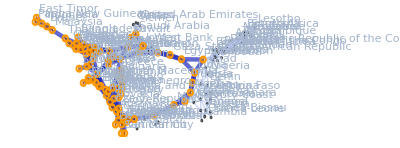
<|CostValue→6,EdgeList→{Switzerland<->France,Switzerland<->Germany,Switzerland<->Liechtenstein,Austria<->Switzerland,Austria<->Germany,Austria<->Italy,Austria<->Liechtenstein,Austria<->Slovenia,Germany<->France,Germany<->Czech Republic,Germany<->Belgium,Germany<->Luxembourg,Germany<->Denmark,Germany<->Netherlands,Italy<->Switzerland,Italy<->France,Italy<->San Marino,Italy<->Vatican City,Liechtenstein<->Switzerland,Liechtenstein<->Austria,Czech Republic<->Austria,Czech Republic<->Germany,Czech Republic<->Slovakia,Hungary<->Austria,Hungary<->Slovenia,Hungary<->Serbia,Hungary<->Ukraine,Slovakia<->Austria,Slovakia<->Czech Republic,Slovakia<->Hungary,Slovenia<->Austria,Slovenia<->Italy,Slovenia<->Croatia,Belgium<->France,Belgium<->Luxembourg,Belgium<->Netherlands,Luxembourg<->France,Luxembourg<->Belgium,Spain<->France,Denmark<->Germany,Netherlands<->Germany,Netherlands<->Belgium,Poland<->Germany,Poland<->Czech Republic,Poland<->Slovakia,Poland<->Ukraine,San Marino<->Italy,Vatican City<->Italy,Croatia<->Slovenia,Croatia<->Serbia,Romania<->Hungary,Romania<->Serbia,Romania<->Ukraine,Serbia<->Hungary,Serbia<->Croatia,Serbia<->Romania,Serbia<->Bosnia and Herzegovina,Serbia<->Montenegro,Serbia<->Bulgaria,Serbia<->North Macedonia,Ukraine<->Hungary,Ukraine<->Slovakia,Ukraine<->Poland,Ukraine<->Romania,Ukraine<->Belarus,Ukraine<->Moldova,Belarus<->Poland,Belarus<->Ukraine,Belarus<->Latvia,Lithuania<->Poland,Lithuania<->Belarus,Russia<->Poland,Russia<->Ukraine,Russia<->Belarus,Russia<->Lithuania,Russia<->Latvia,Russia<->Azerbaijan,Russia<->Estonia,Russia<->Finland,Russia<->Georgia,Morocco<->Spain,Morocco<->Western Sahara,Latvia<->Lithuania,Latvia<->Russia,Latvia<->Estonia,Bosnia and Herzegovina<->Serbia,Bosnia and Herzegovina<->Montenegro,Montenegro<->Bosnia and Herzegovina,Montenegro<->Kosovo,Montenegro<->Albania,Algeria<->Morocco,Algeria<->Western Sahara,Algeria<->Libya,Western Sahara<->Morocco,Western Sahara<->Algeria,Bulgaria<->Romania,Bulgaria<->Serbia,Bulgaria<->North Macedonia,Moldova<->Ukraine,Azerbaijan<->Russia,Azerbaijan<->Georgia,Azerbaijan<->Armenia,Azerbaijan<->Iran,Azerbaijan<->Turkey,China<->Russia,China<->Kazakhstan,China<->Mongolia,China<->North Korea,China<->Afghanistan,China<->Bhutan,China<->India,China<->Kyrgyzstan,China<->Laos,China<->Pakistan,China<->Tajikistan,China<->Vietnam,Estonia<->Russia,Estonia<->Latvia,Finland<->Russia,Finland<->Norway,Finland<->Sweden,Georgia<->Russia,Georgia<->Azerbaijan,Georgia<->Turkey,Kazakhstan<->Russia,Kazakhstan<->Turkmenistan,Kazakhstan<->Uzbekistan,Mongolia<->Russia,North Korea<->Russia,North Korea<->South Korea,Norway<->Finland,Kosovo<->Serbia,North Macedonia<->Serbia,North Macedonia<->Albania,Libya<->Algeria,Libya<->Tunisia,Libya<->Egypt,Tunisia<->Algeria,Armenia<->Azerbaijan,Armenia<->Georgia,Iran<->Azerbaijan,Iran<->Armenia,Iran<->Turkey,Iran<->Pakistan,Iran<->Iraq,Turkey<->Bulgaria,Turkey<->Azerbaijan,Turkey<->Iraq,Turkey<->Syria,Greece<->Bulgaria,Afghanistan<->China,Afghanistan<->Iran,Afghanistan<->Tajikistan,Afghanistan<->Turkmenistan,Afghanistan<->Uzbekistan,Bhutan<->India,India<->China,India<->Nepal,India<->Pakistan,India<->Bangladesh,Kyrgyzstan<->Kazakhstan,Kyrgyzstan<->Tajikistan,Kyrgyzstan<->Uzbekistan,Laos<->Myanmar,Laos<->Vietnam,Laos<->Cambodia,Laos<->Thailand,Myanmar<->China,Myanmar<->India,Myanmar<->Bangladesh,Nepal<->China,Pakistan<->China,Pakistan<->Iran,Pakistan<->Afghanistan,Tajikistan<->China,Tajikistan<->Afghanistan,Tajikistan<->Kyrgyzstan,Tajikistan<->Uzbekistan,Vietnam<->Laos,Vietnam<->Cambodia,Sweden<->Finland,Turkmenistan<->Kazakhstan,Turkmenistan<->Iran,Turkmenistan<->Afghanistan,Uzbekistan<->Afghanistan,Uzbekistan<->Kyrgyzstan,Uzbekistan<->Tajikistan,Uzbekistan<->Turkmenistan,Albania<->Montenegro,Albania<->Greece,South Korea<->North Korea,Bangladesh<->India,Bangladesh<->Myanmar,Iraq<->Iran,Iraq<->Turkey,Iraq<->Saudi Arabia,Cambodia<->Laos,Cambodia<->Thailand,Thailand<->Laos,Thailand<->Myanmar,Thailand<->Malaysia,Egypt<->Libya,Egypt<->Sudan,Egypt<->Israel,Sudan<->Libya,Syria<->Israel,Gaza Strip<->Egypt,Israel<->Egypt,Israel<->Gaza Strip,Israel<->Jordan,Jordan<->Iraq,Jordan<->Israel,Kuwait<->Saudi Arabia,Saudi Arabia<->Jordan,Saudi Arabia<->Kuwait,Malaysia<->Thailand,Malaysia<->Brunei,Malaysia<->Indonesia,Brunei<->Malaysia,Indonesia<->Malaysia,Indonesia<->East Timor,Indonesia<->Papua New Guinea,East Timor<->Indonesia,Papua New Guinea<->Indonesia},FlowGraph→-Graphics-,FlowMatrix→SparseArray[…],FlowTable→OptimumFlowData[…][FlowTable],FlowValue→6,Properties→{CostValue,EdgeList,FlowGraph,FlowMatrix,FlowTable,FlowValue,Properties,ResidualGraph,VertexList},ResidualGraph→OptimumFlowData[…][ResidualGraph],VertexList→{Switzerland,Austria,France,Germany,Italy,Liechtenstein,Czech Republic,Hungary,Slovakia,Slovenia,Andorra,Belgium,Luxembourg,Monaco,Spain,Denmark,Netherlands,Poland,San Marino,Vatican City,Croatia,Romania,Serbia,Ukraine,Belarus,Lithuania,Russia,Gibraltar,Morocco,Portugal,Latvia,Bosnia and Herzegovina,Montenegro,Algeria,Western Sahara,Bulgaria,Moldova,Azerbaijan,China,Estonia,Finland,Georgia,Kazakhstan,Mongolia,North Korea,Norway,Kosovo,North Macedonia,Libya,Mali,Mauritania,Niger,Tunisia,Armenia,Iran,Turkey,Greece,Afghanistan,Bhutan,India,Kyrgyzstan,Laos,Myanmar,Nepal,Pakistan,Tajikistan,Vietnam,Sweden,Turkmenistan,Uzbekistan,Albania,South Korea,Bangladesh,Iraq,Cambodia,Thailand,Chad,Egypt,Sudan,Burkina Faso,Guinea,Ivory Coast,Senegal,Benin,Nigeria,Syria,Togo,Ghana,Cameroon,Central African Republic,Gaza Strip,Israel,Guinea-Bissau,Liberia,Sierra Leone,Jordan,Kuwait,Saudi Arabia,Gambia,Eritrea,Ethiopia,South Sudan,Lebanon,Malaysia,Equatorial Guinea,Gabon,Republic of the Congo,Democratic Republic of the Congo,Djibouti,Kenya,Somalia,West Bank,Brunei,Indonesia,Oman,Qatar,United Arab Emirates,Yemen,Uganda,Angola,Burundi,Rwanda,Tanzania,Zambia,East Timor,Papua New Guinea,Namibia,Malawi,Mozambique,Botswana,Zimbabwe,South Africa,Eswatini,Lesotho}|>

```mathematica
AssociationMap[ℱ[#]&,ℱ["Properties"]]
```

```mathematica
places=CountryData["Countries"];
```

7